# This program gives the metric transformation, maps of geodesics and wave equation between different coordinate systems

```mathematica
ClearAll["Global`*"]
```

```mathematica
Quiet@Block[{Print},<<xAct`xCoba`]
Quiet@Block[{Print},<<xAct`xTras`]
Quiet@Block[{Print},<<xAct`TexAct`]
$DefInfoQ=False;
$CVVerbose=False;
SetOptions[AutomaticRules,Verbose->False];
$PrePrint=ScreenDollarIndices;
$LargeComponentSize=30000;
```

```mathematica
DefManifold[M,4,IndexRange[a,p]]
DefMetric[-1,metric[-a,-b],CD,SymbolOfCovD ->{":","∇"}, PrintAs -> "g"]
ChristoffelCD[a,-b,-c] // ChristoffelToMetric;
```

## Coordinate transformation from crd1 to crd2, (coordinate system1 ) to (coordinate system2)

```mathematica
DefChart[crd1,M,{0,1,2,3},{T[],R[],Θ[],Φ[]},ChartColor->Red]
DefChart[crd2,M,{0,1,2,3},{t[],r[],θ[],ϕ[]},ChartColor->Red]
crd1tocrd2:={T[]->(r[]^2+t[](1-r[])^2)/(2r[](1-r[])t[]), R[]->(r[]^2-t[](1-r[])^2)/(2r[](1-r[])t[]),Θ[]->θ[],Φ[]->ϕ[]};
crd2tocrd1:={t[]->1/(T[]^2-R[]^2),r[]->1/(1+T[]-R[]),θ[]->Θ[],ϕ[]->Φ[]};
```

```mathematica
crd1221:=Join[ToExpression[StringDelete[ToString[crd1tocrd2, InputForm],"[]"]],ToExpression[StringDelete[ToString[crd2tocrd1, InputForm],"[]"]]]
(*this functions gives me the coordinates and its transformation and will be used in the plots*)
crd[i_,j_]:=crd1221⟦i,j⟧
```

```mathematica
(*Here we are building the Jacobian*)
```

```mathematica
Map[PDcrd2[-a],crd1tocrd2,{2}]//FullSimplify;
```

```mathematica
Map[ToBasis[crd2],%,{2}]//FullSimplify;
```

```mathematica
Refine[ComponentArray@%];
```

```mathematica
%/.Rule->ComponentValue;
```

```mathematica
jacobianmatrix=ToValues@ComponentArray@Basis[-{a,crd2},{b,crd1}];
```

```mathematica
BasisChange->CTensor[jacobianmatrix,{-crd2, crd1}];
```

```mathematica
MatrixForm[jacobianmatrix] ;
FullSimplify[Inverse[jacobianmatrix]];
A=MatrixForm[%]
SetBasisChange[CTensor[jacobianmatrix,{-crd2,crd1}],-crd1]
```

(t (r/(-1+r)+t-t/r) | -r^2 | 0 | 0
t (1/(-1+1/r)+t-t/r) | r^2 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Det[FullSimplify[Inverse[jacobianmatrix]]]//FullSimplify
```

2 (-1+r) r t^2

### Transforming the metric from crd1 to crd2

```mathematica
met=CTensor[{{-1,0,0,0},{0,1,0,0},{0,0,R[]^2,0},{0,0,0,R[]^2 Sin[Θ[]]^2}},{-crd1,-crd1}];
metInv=CTensor[{{-1,0,0,0},{0,1,0,0},{0,0,1/R[]^2,0},{0,0,0,Csc[Θ[]]^2/R[]^2}},{crd1,crd1}];
met[-a,-b]
metInv[a,b]
```

-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | R^2 | 0
0 | 0 | 0 | R^2 Sin[Θ]^2 |   |  
a | b

-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1/R^2 | 0
0 | 0 | 0 | Csc[Θ]^2/R^2 | a | b
  |

```mathematica
metcrd2=ToCTensor[met,{-crd2,-crd2}]/.crd1tocrd2//FullSimplify;
metInvcrd2=ToCTensor[metInv,{crd2,crd2}]/.crd1tocrd2//FullSimplify;
metcrd2[-a,-b]
metInvcrd2[a,b]
```

0 | 1/(2 (-1+r) r t^2) | 0 | 0
1/(2 (-1+r) r t^2) | 1/((-1+r)^2 r^2 t) | 0 | 0
0 | 0 | ((r^2 (-1+t)+t-2 r t)^2)/(4 (-1+r)^2 r^2 t^2) | 0
0 | 0 | 0 | (Sin[θ]^2 (r^2 (-1+t)+t-2 r t)^2)/(4 (-1+r)^2 r^2 t^2) |   |  
a | b

-4 t^3 | 2 (-1+r) r t^2 | 0 | 0
2 (-1+r) r t^2 | 0 | 0 | 0
0 | 0 | (4 (-1+r)^2 r^2 t^2)/((r^2 (-1+t)+t-2 r t)^2) | 0
0 | 0 | 0 | (4 Csc[θ]^2 (-1+r)^2 r^2 t^2)/((r^2 (-1+t)+t-2 r t)^2) | a | b
  |

```mathematica
DefConstantSymbol[a00, PrintAs -> "(ā)_IJ^K00"]
DefConstantSymbol[a01, PrintAs -> "(ā)_IJ^K01"]
DefConstantSymbol[a02, PrintAs -> "(ā)_IJ^K02"]
DefConstantSymbol[a03, PrintAs -> "(ā)_IJ^K03"]
DefConstantSymbol[a10, PrintAs -> "(ā)_IJ^K10"]
DefConstantSymbol[a11, PrintAs -> "(ā)_IJ^K11"]
DefConstantSymbol[a12, PrintAs -> "(ā)_IJ^K12"]
DefConstantSymbol[a13, PrintAs -> "(ā)_IJ^K13"]
DefConstantSymbol[a20, PrintAs -> "(ā)_IJ^K20"]
DefConstantSymbol[a21, PrintAs -> "(ā)_IJ^K21"]
DefConstantSymbol[a22, PrintAs -> "(ā)_IJ^K22"]
DefConstantSymbol[a23, PrintAs -> "(ā)_IJ^K23"]
DefConstantSymbol[a30, PrintAs -> "(ā)_IJ^K30"]
DefConstantSymbol[a31, PrintAs -> "(ā)_IJ^K31"]
DefConstantSymbol[a32, PrintAs -> "(ā)_IJ^K32"]
DefConstantSymbol[a33, PrintAs -> "(ā)_IJ^K33"]


aten=CTensor[{{a00,a01,a02,a03},{a10,a11,a12,a13},{a20,a21,a22,a23},{a30,a31,a32,a33}},{crd1,crd1}];
aten[a,b]
```

(ā)_IJ^K00 | (ā)_IJ^K01 | (ā)_IJ^K02 | (ā)_IJ^K03
(ā)_IJ^K10 | (ā)_IJ^K11 | (ā)_IJ^K12 | (ā)_IJ^K13
(ā)_IJ^K20 | (ā)_IJ^K21 | (ā)_IJ^K22 | (ā)_IJ^K23
(ā)_IJ^K30 | (ā)_IJ^K31 | (ā)_IJ^K32 | (ā)_IJ^K33 | a | b
  |

```mathematica
aIJ=ToCTensor[aten,{crd2,crd2}]/.crd1tocrd2//FullSimplify;
```

```mathematica
aIJ[a,b]
```

t^2 ((((ā)_IJ^K00-(ā)_IJ^K01-(ā)_IJ^K10+(ā)_IJ^K11) r^2)/(-1+r)^2+2 ((ā)_IJ^K00-(ā)_IJ^K11) t+(((ā)_IJ^K00+(ā)_IJ^K01+(ā)_IJ^K10+(ā)_IJ^K11) (-1+r)^2 t^2)/r^2) | ((-(ā)_IJ^K00+(ā)_IJ^K01+(ā)_IJ^K10-(ā)_IJ^K11) r^3 t)/(-1+r)-((ā)_IJ^K00-(ā)_IJ^K01+(ā)_IJ^K10-(ā)_IJ^K11) (-1+r) r t^2 | (((ā)_IJ^K02-(ā)_IJ^K12) r t)/(-1+r)+(((ā)_IJ^K02+(ā)_IJ^K12) (-1+r) t^2)/r | (((ā)_IJ^K03-(ā)_IJ^K13) r t)/(-1+r)+(((ā)_IJ^K03+(ā)_IJ^K13) (-1+r) t^2)/r
((-(ā)_IJ^K00+(ā)_IJ^K01+(ā)_IJ^K10-(ā)_IJ^K11) r^3 t)/(-1+r)-((ā)_IJ^K00+(ā)_IJ^K01-(ā)_IJ^K10-(ā)_IJ^K11) (-1+r) r t^2 | ((ā)_IJ^K00-(ā)_IJ^K01-(ā)_IJ^K10+(ā)_IJ^K11) r^4 | (-(ā)_IJ^K02+(ā)_IJ^K12) r^2 | (-(ā)_IJ^K03+(ā)_IJ^K13) r^2
(((ā)_IJ^K20-(ā)_IJ^K21) r t)/(-1+r)+(((ā)_IJ^K20+(ā)_IJ^K21) (-1+r) t^2)/r | (-(ā)_IJ^K20+(ā)_IJ^K21) r^2 | (ā)_IJ^K22 | (ā)_IJ^K23
(((ā)_IJ^K30-(ā)_IJ^K31) r t)/(-1+r)+(((ā)_IJ^K30+(ā)_IJ^K31) (-1+r) t^2)/r | (-(ā)_IJ^K30+(ā)_IJ^K31) r^2 | (ā)_IJ^K32 | (ā)_IJ^K33 | a | b
  |

```mathematica
Collect[((2r[](1-r[])t[])/(r[]^2-(1-r[])^2 t[]))^2 aIJ[{0,crd2},{2,crd2}],{a02,a12},FullSimplify]
```

(4 (ā)_IJ^K02 (-1+r) r t^3 (r^2+(-1+r)^2 t))/((r^2 (-1+t)+t-2 r t)^2)+(4 (ā)_IJ^K12 (-1+r) r t^3)/(r^2 (-1+t)+t-2 r t)

```mathematica
nullcon:={a00->-1,a01->1,a02->1,a03->1,a10->-1,a11->1,a12->1,a13->1,a20->-1,a21->-1,a22->1,a23->1,a30->1,a31->-1,a32->-1,a33->1 }
```

```mathematica
Collect[aIJ[{0,crd2},{0,crd2}],{t[],r[]},Simplify]
```

t^2 ((((ā)_IJ^K00-(ā)_IJ^K01-(ā)_IJ^K10+(ā)_IJ^K11) r^2)/(-1+r)^2+2 ((ā)_IJ^K00-(ā)_IJ^K11) t+(((ā)_IJ^K00+(ā)_IJ^K01+(ā)_IJ^K10+(ā)_IJ^K11) (-1+r)^2 t^2)/r^2)

```mathematica
Collect[Expand[Numerator[aIJ[{0,crd2},{0,crd2}]]],{t[],r[]},FullSimplify]/.nullcon//FullSimplify
```

-4 t^3

```mathematica
Collect[Expand[Numerator[aIJ[{0,crd2},{1,crd2}]]],{t[],r[]},FullSimplify]
```

-((ā)_IJ^K00 r^3 t)/(-1+r)+((ā)_IJ^K01 r^3 t)/(-1+r)+((ā)_IJ^K10 r^3 t)/(-1+r)-((ā)_IJ^K11 r^3 t)/(-1+r)+(ā)_IJ^K00 r t^2-(ā)_IJ^K01 r t^2+(ā)_IJ^K10 r t^2-(ā)_IJ^K11 r t^2-(ā)_IJ^K00 r^2 t^2+(ā)_IJ^K01 r^2 t^2-(ā)_IJ^K10 r^2 t^2+(ā)_IJ^K11 r^2 t^2

```mathematica
Collect[Expand[Numerator[aIJ[{0,crd2},{1,crd2}]]],{t[],r[]},FullSimplify]/.nullcon//FullSimplify
```

4 (-1+r) r t^2

```mathematica
Collect[Expand[Numerator[aIJ[{1,crd2},{1,crd2}]]],{t[],r[]},FullSimplify]
```

((ā)_IJ^K00-(ā)_IJ^K01-(ā)_IJ^K10+(ā)_IJ^K11) r^4

```mathematica
Collect[Expand[Numerator[aIJ[{1,crd2},{1,crd2}]]],{t[],r[]},FullSimplify]/.nullcon//FullSimplify
```

0

```mathematica
Collect[Expand[aIJ[{0,crd2},{2,crd2}]],{t[],r[]},FullSimplify]
```

((ā)_IJ^K02 r t)/(-1+r)-((ā)_IJ^K12 r t)/(-1+r)+(ā)_IJ^K02 t^2+(ā)_IJ^K12 t^2-((ā)_IJ^K02 t^2)/r-((ā)_IJ^K12 t^2)/r

## Geodesics in Minkowski space-time

Here we map the following geodesics in Minkowski space-time   such that -(t̄)^2  +(r̄)^2>0, and we choose   t̄= αr̄- β  where  α, β, take different values depending on the geodesic they represent

The coordinate transformation we are using is of the form
ϕ: M̄→ M= (x^μ)

```mathematica
crd1tocrd2
```

{T→(r^2+(1-r)^2 t)/(2 (1-r) r t),R→(r^2-(1-r)^2 t)/(2 (1-r) r t),Θ→θ,Φ→ϕ}

and the inverse map is given by
ϕ^-1: M →M̄= ((x^-)^μ)

### Space-like geodesics

Here we map the following geodesics in Minkowski space-time   such that -(t̄)^2  +(r̄)^2>0, and we choose   t̄= αr̄- β  where  0<α<1, β=1

```mathematica
pl1=0 ;(*is the plot range *)
```

```mathematica
pl2=1
```

1

```mathematica
β=0.8;
f1=crd[1,1]==crd[2,1];
f2=crd[1,1]==-crd[2,1];
f3=crd[1,2]==crd[2,2];
f4=crd[1,2]==-crd[2,2];

crd[1,2]
```

(r^2+(1-r)^2 t)/(2 (1-r) r t)

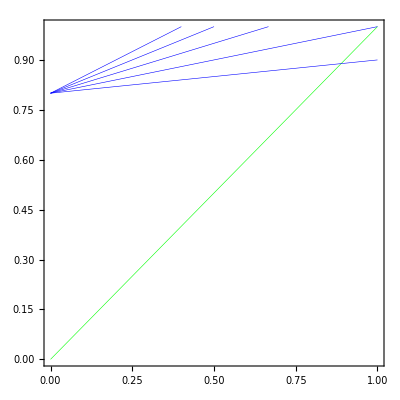

```mathematica
ContourPlot[{Evaluate[{f1,f2}],Evaluate[Map[crd[1,1]==#*crd[2,1]+β&,Range[0.1,0.5,0.1]]]}, {crd[2,1],-pl1,pl2},{crd[1,1],-pl1,pl2}, ContourStyle->{{Green,Thickness[0.001]},{Green,Thickness[0.001]},{Blue,Thickness[0.001]}, {Blue,Thickness[0.001]},{Blue,Thickness[0.001]},{Blue,Thickness[0.001]},{Blue,Thickness[0.001]},{Blue,Thickness[0.001]}}]
```

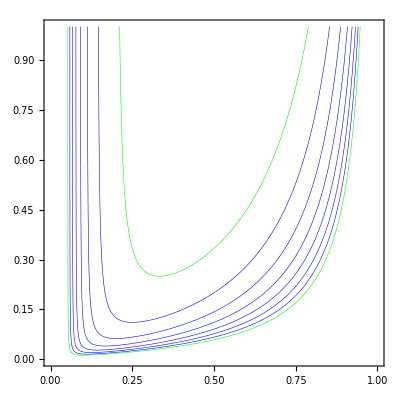

```mathematica
ContourPlot[{ Evaluate[Map[crd[1,2]==#&,Range[1,9,1]]]}, {crd[6,1],-pl1,pl2},{crd[5,1],-pl1,pl2}, ContourStyle->{{Green,Thickness[0.001]},{Green,Thickness[0.001]},{Blue,Thickness[0.001]}, {Blue,Thickness[0.001]},{Blue,Thickness[0.001]},{Blue,Thickness[0.001]},{Blue,Thickness[0.001]},{Blue,Thickness[0.001]}},PlotPoints->50]
```

### Null Geodesics

Here we plot the null geodesics  t̄= α r̄+ β  where  α=1, β∈[0,3]

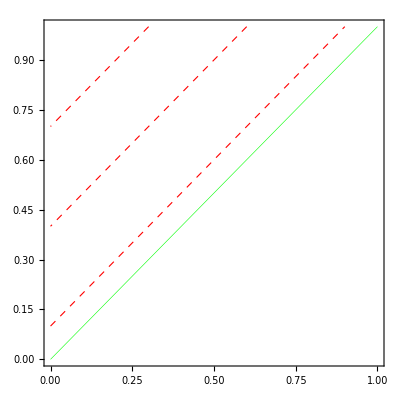

```mathematica
ContourPlot[{Evaluate[{f1,f2}],Evaluate[Map[crd[1,1]==crd[2,1]+#&,Range[0.1,3,0.3]]]}, {crd[2,1],-pl1,pl2},{crd[1,1],-pl1,pl2}, PlotRange->{{-pl1,pl2},{-pl1,pl2}}, ContourStyle->{{Green,Thickness[0.001]},{Green,Thickness[0.001]},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed}},Frame->True,PlotPoints->80]
```

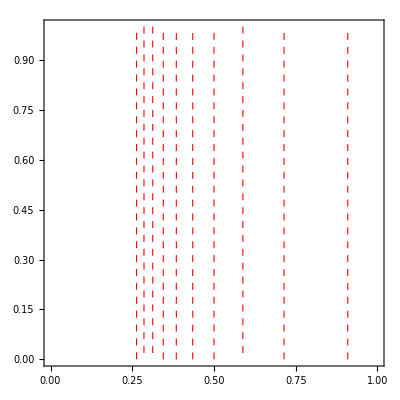

```mathematica
ContourPlot[{Evaluate[{f3,f4}],Evaluate[Map[crd[1,2]==crd[2,2]+#&,Range[0.1,3,0.3]]]}, {crd[6,1],-pl1,pl2},{crd[5,1],-pl1,pl2}, PlotRange->{{-pl1,pl2},{-pl1,pl2}}, ContourStyle->{{Green,Thickness[0.001]},{Green,Thickness[0.001]},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed}},Frame->True,PlotPoints->20]
```

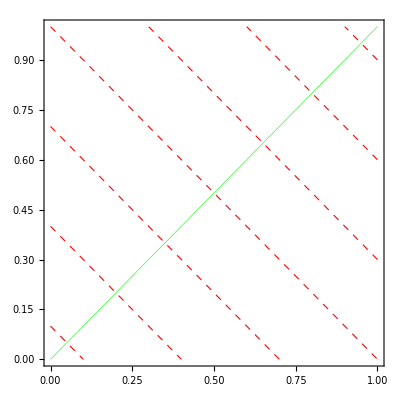

```mathematica
ContourPlot[{Evaluate[{f1,f2}],Evaluate[Map[crd[1,1]==-crd[2,1]+#&,Range[0.1,3,0.3]]]}, {crd[2,1],-pl1,pl2},{crd[1,1],-pl1,pl2}, PlotRange->{{-pl1,pl2},{-pl1,pl2}}, ContourStyle->{{Green,Thickness[0.001]},{Green,Thickness[0.001]},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed}},Frame->True]
```

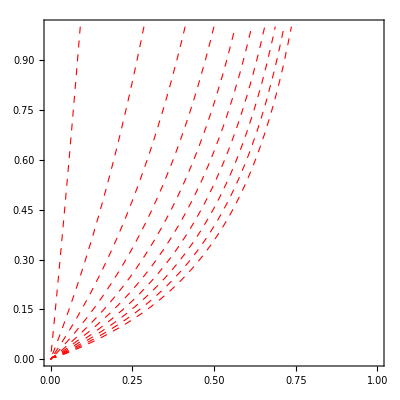

```mathematica
ContourPlot[{Evaluate[{f3,f4}],Evaluate[Map[crd[1,2]==-crd[2,2]+#&,Range[0.1,3,0.3]]]}, {crd[6,1],-pl1,pl2},{crd[5,1],-pl1,pl2}, PlotRange->{{-pl1,pl2},{-pl1,pl2}}, ContourStyle->{{Green,Thickness[0.001]},{Green,Thickness[0.001]},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed}},Frame->True,PlotPoints->20]
```

### Time -like geodesics

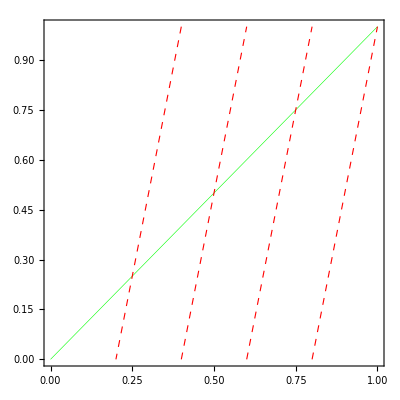

```mathematica
ContourPlot[{Evaluate[{f1,f2}],Evaluate[Map[crd[1,1]==5crd[2,1]-#&,Range[1,5,1]]]}, {crd[2,1],-pl1,pl2},{crd[1,1],-pl1,pl2}, PlotRange->{{-pl1,pl2},{-pl1,pl2}}, ContourStyle->{{Green,Thickness[0.001]},{Green,Thickness[0.001]},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed}},Frame->True]
```

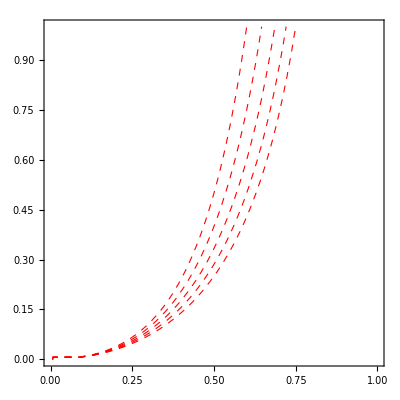

```mathematica
ContourPlot[{Evaluate[{f3,f4}],Evaluate[Map[crd[1,2]==5crd[2,2]-#&,Range[1,5,1]]]}, {crd[6,1],-pl1,pl2},{crd[5,1],-pl1,pl2}, PlotRange->{{-pl1,pl2},{-pl1,pl2}}, ContourStyle->{{Green,Thickness[0.001]},{Green,Thickness[0.001]},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed}},Frame->True,PlotPoints->20]
```

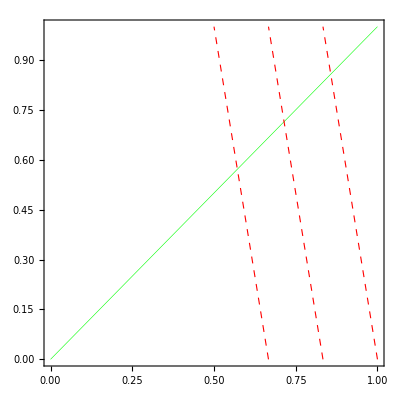

```mathematica
ContourPlot[{Evaluate[{f1,f2}],Evaluate[Map[crd[1,1]==-6crd[2,1]+#&,Range[4,9,1]]]}, {crd[2,1],-pl1,pl2},{crd[1,1],-pl1,pl2}, PlotRange->{{-pl1,pl2},{-pl1,pl2}}, ContourStyle->{{Green,Thickness[0.001]},{Green,Thickness[0.001]},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed}},Frame->True]
```

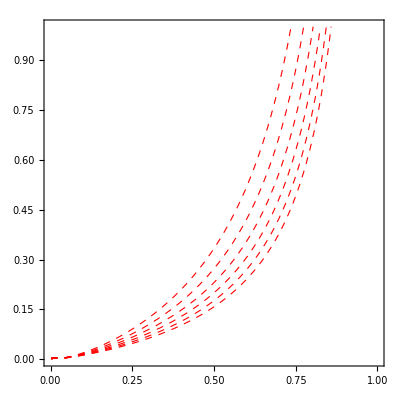

```mathematica
ContourPlot[{Evaluate[{f3,f4}],Evaluate[Map[crd[1,2]==-2crd[2,2]+#&,Range[4,9,1]]]}, {crd[6,1],-pl1,pl2},{crd[5,1],-pl1,pl2}, PlotRange->{{-pl1,pl2},{-pl1,pl2}}, ContourStyle->{{Green,Thickness[0.001]},{Green,Thickness[0.001]},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed},{Red,Thickness[0.002],Dashed}},Frame->True,PlotPoints->30]
```

## The wave equation

```mathematica
TableOfComponents[metcrd2[-a,-b],{-a,-crd2},{-b,-crd2}] //FullSimplify(*This is a remainder of what the metric is*)
```

{{0,1/(2 (-1+r) r t^2),0,0},{1/(2 (-1+r) r t^2),1/((-1+r)^2 r^2 t),0,0},{0,0,((r^2 (-1+t)+t-2 r t)^2)/(4 (-1+r)^2 r^2 t^2),0},{0,0,0,(Sin[θ]^2 (r^2 (-1+t)+t-2 r t)^2)/(4 (-1+r)^2 r^2 t^2)}}

```mathematica
(*From the line above facorize the conformal factor and enter the resulting metric*)
```

```mathematica
MatrixForm[conformal={
{0,-(2r[](1-r[]))/((r[]^2-t[](1-r[])^2)^2),0,0},
{-(2r[](1-r[]))/((r[]^2-t[](1-r[])^2)^2),(4t[])/((r[]^2-t[](1-r[])^2)^2),0,0},
{0,0,1,0},
{0,0,0,Sin[θ[]]^2}
}]
```

(0 | -(2 (1-r) r)/((r^2-(1-r)^2 t)^2) | 0 | 0
-(2 (1-r) r)/((r^2-(1-r)^2 t)^2) | (4 t)/((r^2-(1-r)^2 t)^2) | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | Sin[θ]^2)

```mathematica
MetricInBasis[metric,-crd2,conformal];
```

```mathematica
TableOfComponents[metric[-a,-b],{-a,-crd2},{-b,-crd2}]// ToValues //MatrixForm
```

(0 | (2 (-1+r) r)/((r^2 (-1+t)+t-2 r t)^2) | 0 | 0
(2 (-1+r) r)/((r^2 (-1+t)+t-2 r t)^2) | (4 t)/((r^2 (-1+t)+t-2 r t)^2) | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | Sin[θ]^2)

```mathematica
MetricCompute[metric,crd2,All,CVSimplify->Simplify,Verbose->False]
```

Inverse metric

```mathematica
TableOfComponents[metric[a,b],{a,crd2},{b,crd2}]// ToValues //MatrixForm
```

(-(t (r^2 (-1+t)+t-2 r t)^2)/((-1+r)^2 r^2) | ((r^2 (-1+t)+t-2 r t)^2)/(2 (-1+r) r) | 0 | 0
((r^2 (-1+t)+t-2 r t)^2)/(2 (-1+r) r) | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | Csc[θ]^2)

Christoffel symbols

```mathematica
TableOfComponents[ToBasis[crd2][Christoffel[CD,PDcrd2][a,-b,-c]],{a,crd2},{-b,-crd2},{-c,-crd2}] // ToValues ;
```

```mathematica
TableOfComponents[ChristoffelCDPDcrd2[a,-b,-c],{a,crd2},{-b,-crd2},{-c,-crd2}]  // ToValues;
```

```mathematica
TableOfComponents[ChristoffelCDPDcrd2[a,-b,-c],{a,crd2},{-b,-crd2},{-c,-crd2}] [[4,3,4]] // ToValues
```

Cot[θ]

Ricci Scalar

```mathematica
ToBasis[crd2][RicciScalarCD[]] // ToValues
```

0

```mathematica
TableOfComponents[ToBasis[crd2][RicciCD[-a,-b]],{-a,-crd2},{-b,-crd2}] // ToValues // MatrixForm
```

(0 | -(2 (-1+r) r)/((r^2 (-1+t)+t-2 r t)^2) | 0 | 0
-(2 (-1+r) r)/((r^2 (-1+t)+t-2 r t)^2) | -(4 t)/((r^2 (-1+t)+t-2 r t)^2) | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | Sin[θ]^2)

```mathematica
ToBasis[crd2][Detmetric[]] // ToValues
```

-(4 (-1+r)^2 r^2 Sin[θ]^2)/((r^2 (-1+t)+t-2 r t)^4)

## Defining the Conformal Wave Equation

Defining the conformal factor

```mathematica
DefTensor[Ω[],M]
```

```mathematica
DefScalarFunction[ω]
```

```mathematica
ComponentValue[Ω[],ω[t[],r[]]]
```

Ω→ω[t,r]

```mathematica
(*Enter here the conformal factor*)
```

```mathematica
ω[x_,y_] := (y^2-x(1-y)^2)/(2x*y(1-y))
```

```mathematica
Ω[] // ToValues
```

(r^2-(1-r)^2 t)/(2 (1-r) r t)

```mathematica
ChangeCovD[CD[-a][Ω[]],CD,PDcrd2];
```

```mathematica
TableOfComponents[ChangeCovD[CD[-a][Ω[]],CD,PDcrd2] ,{-a,-crd2}]  // ToValues // Simplify
```

{r/(2 (-1+r) t^2),(t-2 r t+r^2 (1+t))/(2 (-1+r)^2 r^2 t),0,0}

```mathematica
TableOfComponents[ChangeCovD[CD[a][Ω[]],CD,PDcrd2] ,{a,crd2}]  // ToValues // ToValues // Simplify;
```

Wave variable

```mathematica
DefTensor[u[],M]
```

```mathematica
TableOfComponents[ChristoffelCDPDcrd2[a,-b,-c],{a,crd2},{-b,-crd2},{-c,-crd2}]  // ToValues
```

{{{-(2 (-1+r)^2)/(r^2 (-1+t)+t-2 r t),-(t-2 r t+r^2 (1+t))/((-1+r) r (r^2 (-1+t)+t-2 r t)),0,0},{-(t-2 r t+r^2 (1+t))/((-1+r) r (r^2 (-1+t)+t-2 r t)),0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,(2 (r+t-r t))/(r^2 (-1+t)+t-2 r t),0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-Cos[θ] Sin[θ]}},{{0,0,0,0},{0,0,0,0},{0,0,0,Cot[θ]},{0,0,Cot[θ],0}}}

```mathematica
coord:={t,r,θ,ϕ}
```

```mathematica
affine:=affine=Simplify[TableOfComponents[ChristoffelCDPDcrd2[a,-b,-c],{a,crd2},{-b,-crd2},{-c,-crd2}] // ToValues]
```

```mathematica
listaffine:=Table[If[UnsameQ[affine[[ν,λ,μ]],0],{Style[Subsuperscript[Γ,Row[{coord[[λ]],coord[[μ]]}],coord[[ν]]],18],"=",Style[affine[[ν,λ,μ]],14]},0],{ν,1,4},{λ,1,4},{μ,1,4}]
TableForm[Partition[DeleteCases[Flatten[listaffine],0],3],TableSpacing->{1,2}]
```

Γ_tt^t | = | -(2 (-1+r)^2)/(r^2 (-1+t)+t-2 r t)
Γ_tr^t | = | -(t-2 r t+r^2 (1+t))/((-1+r) r (r^2 (-1+t)+t-2 r t))
Γ_rt^t | = | -(t-2 r t+r^2 (1+t))/((-1+r) r (r^2 (-1+t)+t-2 r t))
Γ_rr^r | = | (2 (r+t-r t))/(r^2 (-1+t)+t-2 r t)
Γ_ϕϕ^θ | = | -Cos[θ] Sin[θ]
Γ_θϕ^ϕ | = | Cot[θ]
Γ_ϕθ^ϕ | = | Cot[θ]

```mathematica
affine[[1,1,1]]
affine[[1,1,2]]
```

-(2 (-1+r)^2)/(r^2 (-1+t)+t-2 r t)

-(t-2 r t+r^2 (1+t))/((-1+r) r (r^2 (-1+t)+t-2 r t))

```mathematica
t[]^2 affine[[1,1,1]]+((2r[](1-r[]))/t[])affine[[1,1,2]]//Simplify
```

(2 (t-t^3+2 r t (-1+t^2)+r^2 (1+t-t^3)))/(t (r^2 (-1+t)+t-2 r t))

Wave equation

```mathematica
ToBasis[crd2][ChangeCovD[metric[a,b] CD[-a][CD[-b][u[]]],CD,PDcrd2]] // TraceBasisDummy // ToValues //FullSimplify
```

((r^2 (-1+t)+t-2 r t)^2 (-2 (𝒟_0 u)-2 t (𝒟_0 𝒟_0 u)+(-1+r) r (𝒟_0 𝒟_1 u+𝒟_1 𝒟_0 u)))/(2 (-1+r)^2 r^2)+Cot[θ] (𝒟_2 u)+𝒟_2 𝒟_2 u+Csc[θ]^2 (𝒟_3 𝒟_3 u)

```mathematica
Simplify[-(2 t (r^2 (-1+t)+t-2 r t))/r^2+((r^2 (-1+t)+t-2 r t) (t-2 r t+r^2 (1+t)))/((-1+r)^2 r^2) ]
```

-((r^2 (-1+t)+t-2 r t)^2)/((-1+r)^2 r^2)

```mathematica
Grad[(r^2-(1-r)^2 t)/(2 (1-r) r *t),{t,r}]//FullSimplify
```

{r/(2 (-1+r) t^2),1/2 (1/r^2+1/((-1+r)^2 t))}

```mathematica
Collect[Expand[(-r[]/(2(1-r[])t[]^2))^2 aIJ[{0,crd2},{0,crd2}]-(aIJ[{0,crd2},{1,crd2}]+aIJ[{1,crd2},{0,crd2}])(r[]/(2(1-r[])t[]^2))*((r[]^2+(1-r[])^2 t[])/(2 r[]^2(1-r[])^2 t[]))+aIJ[{1,crd2},{1,crd2}]((r[]^2+(1-r[])^2 t[])/(2 r[]^2(1-r[])^2 t[]))^2],{t[]}]//Simplify
```

(ā)_IJ^K11

```mathematica
(-r[]/(2(1-r[])t[]^2))^2 aIJ[{0,crd2},{0,crd2}]-(aIJ[{0,crd2},{1,crd2}]+aIJ[{1,crd2},{0,crd2}])(r[]/(2(1-r[])t[]^2))*((r[]^2+(1-r[])^2 t[])/(2 r[]^2(1-r[])^2 t[]))+aIJ[{1,crd2},{1,crd2}]((r[]^2+(1-r[])^2 t[])/(2 r[]^2(1-r[])^2 t[]))^2//FullSimplify
```

(ā)_IJ^K11

```mathematica
D[1/(r(1-r)),r]//FullSimplify
```

1/(-1+r)^2-1/r^2

```mathematica
ToBasis[crd2][ChangeCovD[Ω[]^-2 metric[a,b] CD[-a][CD[-b][u[]]],CD,PDcrd2]] // TraceBasisDummy // ToValues
```

-(8 (1-r)^2 t^3 (r^2 (-1+t)+t-2 r t) (𝒟_0 u))/((r^2-(1-r)^2 t)^2)+(4 (1-r)^2 t^2 (r^2 (-1+t)+t-2 r t) (t-2 r t+r^2 (1+t)) (𝒟_0 u))/((-1+r)^2 (r^2-(1-r)^2 t)^2)-(4 (1-r)^2 t^3 (r^2 (-1+t)+t-2 r t)^2 (𝒟_0 𝒟_0 u))/((-1+r)^2 (r^2-(1-r)^2 t)^2)+(2 (1-r)^2 r t^2 (r^2 (-1+t)+t-2 r t)^2 (𝒟_0 𝒟_1 u))/((-1+r) (r^2-(1-r)^2 t)^2)+(2 (1-r)^2 r t^2 (r^2 (-1+t)+t-2 r t)^2 (𝒟_1 𝒟_0 u))/((-1+r) (r^2-(1-r)^2 t)^2)+(4 Cot[θ] (1-r)^2 r^2 t^2 (𝒟_2 u))/((r^2-(1-r)^2 t)^2)+(4 (1-r)^2 r^2 t^2 (𝒟_2 𝒟_2 u))/((r^2-(1-r)^2 t)^2)+(4 Csc[θ]^2 (1-r)^2 r^2 t^2 (𝒟_3 𝒟_3 u))/((r^2-(1-r)^2 t)^2)

```mathematica
FullSimplify[(2 (1-r) r t t (r^2 (-1+t)+t-2 r t)^2)/((r^2-(1-r)^2 t) (-1+r)^2 r^2)]
```

(2 (-1+r) r t t (r^2 (-1+t)+t-2 r t)^2)/((r^2 (-1+t)+t-2 r t) (-1+r)^2 r^2)

Semilinear part

```mathematica
ToBasis[crd2][ChangeCovD[aIJ[{0,crd2},{0,crd2}]CD[{0,-crd2}][Ω[]]+aIJ[{0,crd2},{1,crd2}]CD[{1,-crd2}][Ω[]],CD,PDcrd2]]//TraceBasisDummy //ToValues//FullSimplify
```

(((ā)_IJ^K01-(ā)_IJ^K11) r t)/(-1+r)+(((ā)_IJ^K01+(ā)_IJ^K11) (-1+r) t^2)/r

```mathematica
ToBasis[crd2][ChangeCovD[aIJ[{0,crd2},{0,crd2}]CD[{0,-crd2}][Ω[]]+aIJ[{1,crd2},{0,crd2}]CD[{1,-crd2}][Ω[]],CD,PDcrd2]]//TraceBasisDummy //ToValues//FullSimplify
```

(((ā)_IJ^K10-(ā)_IJ^K11) r t)/(-1+r)+(((ā)_IJ^K10+(ā)_IJ^K11) (-1+r) t^2)/r

```mathematica
ToBasis[crd2][ChangeCovD[aIJ[{1,crd2},{0,crd2}]CD[{0,-crd2}][Ω[]]+aIJ[{1,crd2},{1,crd2}]CD[{1,-crd2}][Ω[]],CD,PDcrd2]]//TraceBasisDummy //ToValues//FullSimplify
```

(-(ā)_IJ^K01+(ā)_IJ^K11) r^2

```mathematica
ToBasis[crd2][ChangeCovD[aIJ[{0,crd2},{1,crd2}]CD[{0,-crd2}][Ω[]]+aIJ[{1,crd2},{1,crd2}]CD[{1,-crd2}][Ω[]],CD,PDcrd2]]//TraceBasisDummy //ToValues//FullSimplify
```

(-(ā)_IJ^K10+(ā)_IJ^K11) r^2

```mathematica
ToBasis[crd2][ChangeCovD[aIJ[{2,crd2},{0,crd2}]CD[{0,-crd2}][Ω[]]+aIJ[{2,crd2},{1,crd2}]CD[{1,-crd2}][Ω[]],CD,PDcrd2]]//TraceBasisDummy //ToValues//FullSimplify
```

(ā)_IJ^K21

```mathematica
ToBasis[crd2][ChangeCovD[aIJ[{3,crd2},{0,crd2}]CD[{0,-crd2}][Ω[]]+aIJ[{3,crd2},{1,crd2}]CD[{1,-crd2}][Ω[]],CD,PDcrd2]]//TraceBasisDummy //ToValues//FullSimplify
```

(ā)_IJ^K31

```mathematica
ToBasis[crd2][ChangeCovD[aIJ[{0,crd2},{2,crd2}]CD[{0,-crd2}][Ω[]]+aIJ[{1,crd2},{2,crd2}]CD[{1,-crd2}][Ω[]],CD,PDcrd2]]//TraceBasisDummy //ToValues//FullSimplify
```

(ā)_IJ^K12

```mathematica
ToBasis[crd2][ChangeCovD[aIJ[{0,crd2},{3,crd2}]CD[{0,-crd2}][Ω[]]+aIJ[{1,crd2},{3,crd2}]CD[{1,-crd2}][Ω[]],CD,PDcrd2]]//TraceBasisDummy //ToValues//FullSimplify
```

(ā)_IJ^K13

```mathematica
ToBasis[crd2][ChangeCovD[aIJ[{0,crd2},{0,crd2}](CD[{0,-crd2}][Ω[]])^2+(aIJ[{1,crd2},{0,crd2}]+aIJ[{0,crd2},{1,crd2}])CD[{0,-crd2}][Ω[]]CD[{1,-crd2}][Ω[]]+aIJ[{1,crd2},{1,crd2}](CD[{1,-crd2}][Ω[]])^2,CD,PDcrd2]]//TraceBasisDummy //ToValues//FullSimplify
```

(ā)_IJ^K11

Linear terms from the quasilinear part

```mathematica
DefConstantSymbol[h00, PrintAs -> "(h̄)_I^00"]
DefConstantSymbol[h01, PrintAs -> "(h̄)_I^01"]
DefConstantSymbol[h02, PrintAs -> "(h̄)_I^02"]
DefConstantSymbol[h03, PrintAs -> "(h̄)_I^03"]
DefConstantSymbol[h10, PrintAs -> "(h̄)_I^10"]
DefConstantSymbol[h11, PrintAs -> "(h̄)_I^11"]
DefConstantSymbol[h12, PrintAs -> "(h̄)_I^12"]
DefConstantSymbol[h13, PrintAs -> "(h̄)_I^13"]
DefConstantSymbol[h20, PrintAs -> "(h̄)_I^20"]
DefConstantSymbol[h21, PrintAs -> "(h̄)_I^21"]
DefConstantSymbol[h22, PrintAs -> "(h̄)_I^22"]
DefConstantSymbol[h23, PrintAs -> "(h̄)_I^23"]
DefConstantSymbol[h30, PrintAs -> "(h̄)_I^30"]
DefConstantSymbol[h31, PrintAs -> "(h̄)_I^31"]
DefConstantSymbol[h32, PrintAs -> "(h̄)_I^32"]
DefConstantSymbol[h33, PrintAs -> "(h̄)_I^33"]
```

```mathematica
hten=CTensor[{{h00,h01,h02,h03},{h10,h11,h12,h13},{h20,h21,h22,h23},{h30,h31,h32,h33}},{crd1,crd1}];
hten[a,b]
```

(h̄)_I^00 | (h̄)_I^01 | (h̄)_I^02 | (h̄)_I^03
(h̄)_I^10 | (h̄)_I^11 | (h̄)_I^12 | (h̄)_I^13
(h̄)_I^20 | (h̄)_I^21 | (h̄)_I^22 | (h̄)_I^23
(h̄)_I^30 | (h̄)_I^31 | (h̄)_I^32 | (h̄)_I^33 | a | b
  |

```mathematica
hIJ=ToCTensor[hten,{crd2,crd2}]/.crd1tocrd2//FullSimplify;
```

```mathematica
hIJ[a,b]
```

t^2 ((((h̄)_I^00-(h̄)_I^01-(h̄)_I^10+(h̄)_I^11) r^2)/(-1+r)^2+2 ((h̄)_I^00-(h̄)_I^11) t+(((h̄)_I^00+(h̄)_I^01+(h̄)_I^10+(h̄)_I^11) (-1+r)^2 t^2)/r^2) | ((-(h̄)_I^00+(h̄)_I^01+(h̄)_I^10-(h̄)_I^11) r^3 t)/(-1+r)-((h̄)_I^00-(h̄)_I^01+(h̄)_I^10-(h̄)_I^11) (-1+r) r t^2 | (((h̄)_I^02-(h̄)_I^12) r t)/(-1+r)+(((h̄)_I^02+(h̄)_I^12) (-1+r) t^2)/r | (((h̄)_I^03-(h̄)_I^13) r t)/(-1+r)+(((h̄)_I^03+(h̄)_I^13) (-1+r) t^2)/r
((-(h̄)_I^00+(h̄)_I^01+(h̄)_I^10-(h̄)_I^11) r^3 t)/(-1+r)-((h̄)_I^00+(h̄)_I^01-(h̄)_I^10-(h̄)_I^11) (-1+r) r t^2 | ((h̄)_I^00-(h̄)_I^01-(h̄)_I^10+(h̄)_I^11) r^4 | (-(h̄)_I^02+(h̄)_I^12) r^2 | (-(h̄)_I^03+(h̄)_I^13) r^2
(((h̄)_I^20-(h̄)_I^21) r t)/(-1+r)+(((h̄)_I^20+(h̄)_I^21) (-1+r) t^2)/r | (-(h̄)_I^20+(h̄)_I^21) r^2 | (h̄)_I^22 | (h̄)_I^23
(((h̄)_I^30-(h̄)_I^31) r t)/(-1+r)+(((h̄)_I^30+(h̄)_I^31) (-1+r) t^2)/r | (-(h̄)_I^30+(h̄)_I^31) r^2 | (h̄)_I^32 | (h̄)_I^33 | a | b
  |

```mathematica
ChangeCovD[CD[{0,-crd2}][Ω[]],CD,PDcrd2]// ToValues //FullSimplify
```

r/(2 (-1+r) t^2)

```mathematica
ChangeCovD[CD[{1,-crd2}][Ω[]],CD,PDcrd2]// ToValues //FullSimplify
```

1/2 (1/r^2+1/((-1+r)^2 t))

```mathematica
ToBasis[crd2][ChangeCovD[4hIJ[{0,crd2},{0,crd2}]CD[{0,-crd2}][Ω[]]+2(hIJ[{0,crd2},{1,crd2}]+hIJ[{1,crd2},{0,crd2}])CD[{1,-crd2}][Ω[]],CD,PDcrd2]] // TraceBasisDummy // ToValues //FullSimplify
```

(2 ((h̄)_I^01+(h̄)_I^10-2 (h̄)_I^11) r t)/(-1+r)+(2 ((h̄)_I^01+(h̄)_I^10+2 (h̄)_I^11) (-1+r) t^2)/r

```mathematica
ToBasis[crd2][ChangeCovD[metric[-a,-b]hIJ[a,b],CD,PDcrd2]] // TraceBasisDummy // ToValues //FullSimplify
```

(h̄)_I^22+(h̄)_I^33 Sin[θ]^2-(4 ((h̄)_I^00-(h̄)_I^11) (-1+r)^2 r^2 t^2)/((r^2 (-1+t)+t-2 r t)^2)

```mathematica
ToBasis[crd2][ChangeCovD[(metric[{0,crd2},{0,crd2}]CD[{0,-crd2}][Ω[]]+metric[{1,crd2},{0,crd2}]CD[{1,-crd2}][Ω[]]),CD,PDcrd2]] // TraceBasisDummy // ToValues //FullSimplify
```

((r^2 (-1+t)+t-2 r t)^3)/(4 (-1+r)^3 r^3 t)

```mathematica
ToBasis[crd2][ChangeCovD[4hIJ[{1,crd2},{1,crd2}]CD[{1,-crd2}][Ω[]]+2(hIJ[{0,crd2},{1,crd2}]+hIJ[{1,crd2},{0,crd2}])CD[{0,-crd2}][Ω[]],CD,PDcrd2]] // TraceBasisDummy // ToValues //FullSimplify
```

-2 ((h̄)_I^01+(h̄)_I^10-2 (h̄)_I^11) r^2

```mathematica
ToBasis[crd2][ChangeCovD[(metric[{0,crd2},{1,crd2}]CD[{0,-crd2}][Ω[]]+metric[{1,crd2},{1,crd2}]CD[{1,-crd2}][Ω[]]),CD,PDcrd2]] // TraceBasisDummy // ToValues //FullSimplify
```

((r^2 (-1+t)+t-2 r t)^2)/(4 (-1+r)^2 t^2)

```mathematica
ToBasis[crd2][ChangeCovD[(hIJ[{0,crd2},{2,crd2}]+hIJ[{2,crd2},{0,crd2}])CD[{0,-crd2}][Ω[]]+(hIJ[{1,crd2},{2,crd2}]+hIJ[{2,crd2},{1,crd2}])CD[{1,-crd2}][Ω[]],CD,PDcrd2]]//ToValues//FullSimplify
```

(h̄)_I^12+(h̄)_I^21

```mathematica
ToBasis[crd2][ChangeCovD[(hIJ[{0,crd2},{3,crd2}]+hIJ[{3,crd2},{0,crd2}])CD[{0,-crd2}][Ω[]]+(hIJ[{1,crd2},{3,crd2}]+hIJ[{3,crd2},{1,crd2}])CD[{1,-crd2}][Ω[]],CD,PDcrd2]]//ToValues//FullSimplify
```

(h̄)_I^13+(h̄)_I^31

```mathematica
CD[-a][CD[-b][Ω[]]]
```

∇_a ∇_b Ω

```mathematica
hIJ[a,b](-Ω[]CD[-a][CD[-b][Ω[]]]+4CD[-a][Ω[]]CD[-b][Ω[]]-metric[-a,-b]metric[c,d]CD[-c][Ω[]]CD[-d][Ω[]])
```

(-Ω ∇_a ∇_b Ω+4 ∇_a Ω ∇_b Ω-g |   |  
a | b g | c | d
  |   ∇_c Ω ∇_d Ω) t^2 ((((h̄)_I^00-(h̄)_I^01-(h̄)_I^10+(h̄)_I^11) r^2)/(-1+r)^2+2 ((h̄)_I^00-(h̄)_I^11) t+(((h̄)_I^00+(h̄)_I^01+(h̄)_I^10+(h̄)_I^11) (-1+r)^2 t^2)/r^2) | ((-(h̄)_I^00+(h̄)_I^01+(h̄)_I^10-(h̄)_I^11) r^3 t)/(-1+r)-((h̄)_I^00-(h̄)_I^01+(h̄)_I^10-(h̄)_I^11) (-1+r) r t^2 | (((h̄)_I^02-(h̄)_I^12) r t)/(-1+r)+(((h̄)_I^02+(h̄)_I^12) (-1+r) t^2)/r | (((h̄)_I^03-(h̄)_I^13) r t)/(-1+r)+(((h̄)_I^03+(h̄)_I^13) (-1+r) t^2)/r
((-(h̄)_I^00+(h̄)_I^01+(h̄)_I^10-(h̄)_I^11) r^3 t)/(-1+r)-((h̄)_I^00+(h̄)_I^01-(h̄)_I^10-(h̄)_I^11) (-1+r) r t^2 | ((h̄)_I^00-(h̄)_I^01-(h̄)_I^10+(h̄)_I^11) r^4 | (-(h̄)_I^02+(h̄)_I^12) r^2 | (-(h̄)_I^03+(h̄)_I^13) r^2
(((h̄)_I^20-(h̄)_I^21) r t)/(-1+r)+(((h̄)_I^20+(h̄)_I^21) (-1+r) t^2)/r | (-(h̄)_I^20+(h̄)_I^21) r^2 | (h̄)_I^22 | (h̄)_I^23
(((h̄)_I^30-(h̄)_I^31) r t)/(-1+r)+(((h̄)_I^30+(h̄)_I^31) (-1+r) t^2)/r | (-(h̄)_I^30+(h̄)_I^31) r^2 | (h̄)_I^32 | (h̄)_I^33 | a | b
  |

```mathematica
ToBasis[crd2][ChangeCovD[hIJ[a,b](-Ω[]CD[-a][CD[-b][Ω[]]]+4CD[-a][Ω[]]CD[-b][Ω[]]-metric[-a,-b]metric[c,d]CD[-c][Ω[]]CD[-d][Ω[]]),CD,PDcrd2]]//TraceBasisDummy //ToValues//Simplify
```

-(-8 (h̄)_I^11 (-1+r)^2 r^2 t^2+(h̄)_I^22 (r^2 (-1+t)+t-2 r t)^2+(h̄)_I^33 Sin[θ]^2 (r^2 (-1+t)+t-2 r t)^2)/(4 (-1+r)^2 r^2 t^2)

```mathematica
hten[a,b]
```

(h̄)_I^00 | (h̄)_I^01 | (h̄)_I^02 | (h̄)_I^03
(h̄)_I^10 | (h̄)_I^11 | (h̄)_I^12 | (h̄)_I^13
(h̄)_I^20 | (h̄)_I^21 | (h̄)_I^22 | (h̄)_I^23
(h̄)_I^30 | (h̄)_I^31 | (h̄)_I^32 | (h̄)_I^33 | a | b
  |

```mathematica
hIJ[a,b](-Ω[]CD[-a][CD[-b][Ω[]]]+4CD[-a][Ω[]]CD[-b][Ω[]]-metric[-a,-b]metric[c,d]CD[-c][Ω[]]CD[-d][Ω[]])
```

(-Ω ∇_a ∇_b Ω+4 ∇_a Ω ∇_b Ω-g |   |  
a | b g | c | d
  |   ∇_c Ω ∇_d Ω) t^2 ((((h̄)_I^00-(h̄)_I^01-(h̄)_I^10+(h̄)_I^11) r^2)/(-1+r)^2+2 ((h̄)_I^00-(h̄)_I^11) t+(((h̄)_I^00+(h̄)_I^01+(h̄)_I^10+(h̄)_I^11) (-1+r)^2 t^2)/r^2) | ((-(h̄)_I^00+(h̄)_I^01+(h̄)_I^10-(h̄)_I^11) r^3 t)/(-1+r)-((h̄)_I^00-(h̄)_I^01+(h̄)_I^10-(h̄)_I^11) (-1+r) r t^2 | (((h̄)_I^02-(h̄)_I^12) r t)/(-1+r)+(((h̄)_I^02+(h̄)_I^12) (-1+r) t^2)/r | (((h̄)_I^03-(h̄)_I^13) r t)/(-1+r)+(((h̄)_I^03+(h̄)_I^13) (-1+r) t^2)/r
((-(h̄)_I^00+(h̄)_I^01+(h̄)_I^10-(h̄)_I^11) r^3 t)/(-1+r)-((h̄)_I^00+(h̄)_I^01-(h̄)_I^10-(h̄)_I^11) (-1+r) r t^2 | ((h̄)_I^00-(h̄)_I^01-(h̄)_I^10+(h̄)_I^11) r^4 | (-(h̄)_I^02+(h̄)_I^12) r^2 | (-(h̄)_I^03+(h̄)_I^13) r^2
(((h̄)_I^20-(h̄)_I^21) r t)/(-1+r)+(((h̄)_I^20+(h̄)_I^21) (-1+r) t^2)/r | (-(h̄)_I^20+(h̄)_I^21) r^2 | (h̄)_I^22 | (h̄)_I^23
(((h̄)_I^30-(h̄)_I^31) r t)/(-1+r)+(((h̄)_I^30+(h̄)_I^31) (-1+r) t^2)/r | (-(h̄)_I^30+(h̄)_I^31) r^2 | (h̄)_I^32 | (h̄)_I^33 | a | b
  |

```mathematica
Collect[((2r[](1-r[])t[])/(r[]^2-(1-r[])t[]))^2 hIJ[{0,crd2},{2,crd2}],{h02,h12},FullSimplify]
```

(4 (h̄)_I^02 (-1+r) r t^3 (r^2+(-1+r)^2 t))/((r^2+(-1+r) t)^2)+(4 (h̄)_I^12 (-1+r) r t^3 (r^2 (-1+t)+t-2 r t))/((r^2+(-1+r) t)^2)

```mathematica
ToBasis[crd2][ChangeCovD[hIJ[a,b](-Ω[]CD[-a][CD[-b][Ω[]]]+4CD[-a][Ω[]]CD[-b][Ω[]]-metric[-a,-b]metric[c,d]CD[-c][Ω[]]CD[-d][Ω[]]),CD,PDcrd2]]//TraceBasisDummy //ToValues//Simplify
```

-(-8 (h̄)_I^11 (-1+r)^2 r^2 t^2+(h̄)_I^22 (r^2 (-1+t)+t-2 r t)^2+(h̄)_I^33 Sin[θ]^2 (r^2 (-1+t)+t-2 r t)^2)/(4 (-1+r)^2 r^2 t^2)

```mathematica
FullSimplify[(hIJ[{0,crd2},{2,crd2}]+hIJ[{2,crd2},{0,crd2}])1/(4 t[]^3)]
```

(((h̄)_I^02-(h̄)_I^12+(h̄)_I^20-(h̄)_I^21) r^2+((h̄)_I^02+(h̄)_I^12+(h̄)_I^20+(h̄)_I^21) (-1+r)^2 t)/(4 (-1+r) r t^2)

```mathematica
ToBasis[crd2][ChangeCovD[Ω[]^-2(hIJ[{0,crd2},{3,crd2}]+hIJ[{3,crd2},{0,crd2}])1/(4 t[]^3),CD,PDcrd2]]//TraceBasisDummy //ToValues//FullSimplify
```

(((h̄)_I^03-(h̄)_I^13+(h̄)_I^30-(h̄)_I^31) (-1+r) r^3+((h̄)_I^03+(h̄)_I^13+(h̄)_I^30+(h̄)_I^31) (-1+r)^3 r t)/((r^2 (-1+t)+t-2 r t)^2)

```mathematica
FullSimplify[((Subscript[h̄, I]^03+Subscript[h̄, I]^30) (-1+r) r^3+(Subscript[h̄, I]^03+Subscript[h̄, I]^30) (-1+r)^3 r t)/((r^2 (-1+t)+t-2 r t)^2)]
```

(((h̄)_I^03+(h̄)_I^30) (-1+r) r (r^2+(-1+r)^2 t))/((r^2 (-1+t)+t-2 r t)^2)

```mathematica
FullSimplify[((-Subscript[h̄, I]^13-Subscript[h̄, I]^31) (-1+r) r^3+(Subscript[h̄, I]^13+Subscript[h̄, I]^31) (-1+r)^3 r t)/((r^2 (-1+t)+t-2 r t)^2)]
```

(((h̄)_I^13+(h̄)_I^31) (-1+r) r)/(r^2 (-1+t)+t-2 r t)

```mathematica
CollectConstants[FullSimplify[Ω[]^-2(hIJ[{0,crd2},{3,crd2}]+hIJ[{3,crd2},{0,crd2}])1/(4 t[]^3)],FullSimplify]
```

(((h̄)_I^03-(h̄)_I^13+(h̄)_I^30-(h̄)_I^31) r^2+((h̄)_I^03+(h̄)_I^13+(h̄)_I^30+(h̄)_I^31) (-1+r)^2 t)/(4 (-1+r) r t^2 Ω^2)

```mathematica
FullSimplify[(hIJ[{1,crd2},{3,crd2}]+hIJ[{3,crd2},{1,crd2}])1/(4 t[]^2)]
```

((-(h̄)_I^03+(h̄)_I^13-(h̄)_I^30+(h̄)_I^31) r^2)/(4 t^2)

```mathematica
FullSimplify[(hIJ[{1,crd2},{2,crd2}]+hIJ[{2,crd2},{1,crd2}])1/(4 t[]^2)]
```

((-(h̄)_I^02+(h̄)_I^12-(h̄)_I^20+(h̄)_I^21) r^2)/(4 t^2)

```mathematica
ToValues[hIJ[{0,crd2},{0,crd2}]/(4 t[]^3)+(hIJ[{0,crd2},{0,crd2}]ChristoffelCDPDcrd2[{0,crd2},{0,-crd2},{0,-crd2}]+(hIJ[{0,crd2},{1,crd2}]+hIJ[{1,crd2},{0,crd2}])ChristoffelCDPDcrd2[{0,crd2},{0,-crd2},{1,-crd2}])1/(4 t[]^2)]//FullSimplify
```

(((h̄)_I^00-(h̄)_I^01-(h̄)_I^10+(h̄)_I^11) r^6+((h̄)_I^00-(h̄)_I^01-(h̄)_I^10+(h̄)_I^11) (-1+r)^2 r^4 t-((h̄)_I^00+(h̄)_I^01+(h̄)_I^10+(h̄)_I^11) (-1+r)^4 r^2 t^2-((h̄)_I^00+(h̄)_I^01+(h̄)_I^10+(h̄)_I^11) (-1+r)^6 t^3)/(4 (-1+r)^2 r^2 t (r^2 (-1+t)+t-2 r t))

```mathematica
FullSimplify[((Subscript[h̄, I]^00-Subscript[h̄, I]^01-Subscript[h̄, I]^10+Subscript[h̄, I]^11) r^6+(Subscript[h̄, I]^00-Subscript[h̄, I]^01-Subscript[h̄, I]^10+Subscript[h̄, I]^11) (-1+r)^2 r^4 t)/(4 (-1+r)^2 r^2 t (r^2 (-1+t)+t-2 r t))]
```

(((h̄)_I^00-(h̄)_I^01-(h̄)_I^10+(h̄)_I^11) r^2 (r^2+(-1+r)^2 t))/(4 (-1+r)^2 t (r^2 (-1+t)+t-2 r t))

```mathematica
FullSimplify[(-(Subscript[h̄, I]^00+Subscript[h̄, I]^01+Subscript[h̄, I]^10+Subscript[h̄, I]^11) (-1+r)^4 r^2 t^2-(Subscript[h̄, I]^00+Subscript[h̄, I]^01+Subscript[h̄, I]^10+Subscript[h̄, I]^11) (-1+r)^6 t^3)/(4 (-1+r)^2 r^2 t (r^2 (-1+t)+t-2 r t))]
```

-(((h̄)_I^00+(h̄)_I^01+(h̄)_I^10+(h̄)_I^11) (-1+r)^2 t (r^2+(-1+r)^2 t))/(-4 r^4+4 (-1+r)^2 r^2 t)

```mathematica
ToValues[(hIJ[{1,crd2},{1,crd2}](1-2r[]))/(4 r[]^2(1-r[])^2 t[])+(1/(4t[]r[](1-r[])))hIJ[{1,crd2},{1,crd2}]ChristoffelCDPDcrd2[{1,crd2},{1,-crd2},{1,-crd2}]]//FullSimplify
```

(((h̄)_I^00-(h̄)_I^01-(h̄)_I^10+(h̄)_I^11) r^2 (r^2+(-1+r)^2 t))/(4 (-1+r)^2 t (r^2 (-1+t)+t-2 r t))

```mathematica
ToBasis[crd2][ChangeCovD[metric[a,b] CD[-a][CD[-b][(r[]^2-t[](1-r[])^2)/(2r[](1-r[])t[])]],CD,PDcrd2]] // TraceBasisDummy // ToValues //FullSimplify
```

0

```mathematica
ToBasis[crd2][ChangeCovD[metric[a,b] CD[-a][CD[-b][(r[]^2+t[](1-r[])^2)/(2r[](1-r[])t[])]],CD,PDcrd2]] // TraceBasisDummy // ToValues //FullSimplify
```

0